```mathematica
Clear["Global`*"]
```

### Calculating displacements correlation for 2 connected particles in 2D (1D x-link). ω0=k/γ

```mathematica
A=ω0({{-1, 0, 1, 0}, {0, 0, 0, 0}, {1, 0, -1, 0}, {0, 1, 0, 0}});
eigsys=Eigensystem[A];
U = eigsys[[2]];
U//MatrixForm
λs=eigsys[[1]]
Um1=Inverse[U];
(*λ=-2 k12/γ;*)
b[1]=Transpose[{{√(2 D1),0,0,0}}];
b[2]=Transpose[{{0, √(2D1),0,0}}];
b[3]=Transpose[{{0, 0,√(2D2),0}}];
b[4]=Transpose[{{0, 0,0,√(2D2)}}];
R0=Transpose[{{R01,R02,R03,R04}}];
a=ω0 L ({{-1}, {0}, {1}, {0}});
```

(0 | -1 | 0 | 1
-1 | 0 | 1 | 0
0 | 1 | 0 | 1
1 | 0 | 1 | 0)

{-2 ω0,-2 ω0,0,0}

### Regular part of the displacement

```mathematica
(*RnRegular=U.DiagonalMatrix[Map[J1[#]&,λs]].Um1.R0+U.DiagonalMatrix[Map[J2[#]&,λs]].Um1.a;
%//MatrixForm*)
```

(R03 (J1[0]/2-1/2 J1[-2 ω0])+R01 (J1[0]/2+1/2 J1[-2 ω0])+L ω0 (J2[0]/2-1/2 J2[-2 ω0])-L ω0 (J2[0]/2+1/2 J2[-2 ω0])
R04 (J1[0]/2-1/2 J1[-2 ω0])+R02 (J1[0]/2+1/2 J1[-2 ω0])
R01 (J1[0]/2-1/2 J1[-2 ω0])+R03 (J1[0]/2+1/2 J1[-2 ω0])-L ω0 (J2[0]/2-1/2 J2[-2 ω0])+L ω0 (J2[0]/2+1/2 J2[-2 ω0])
R02 (J1[0]/2-1/2 J1[-2 ω0])+R04 (J1[0]/2+1/2 J1[-2 ω0]))

### Stochastic part of the displacement J[λ, n] = ∫_0^t_n ⅇ^(λ(t_n-s))ⅆW

```mathematica
f1 = Sum[p[i] U.DiagonalMatrix[Map[J[#,n]&,λs]].Um1.b[i],{i,1,4}]
ξn=RnStochastic=(f1/.n->n+1)-f1
```

{{√2 √D1 (1/2 J[0,n]+1/2 J[-2 ω0,n]) p[1]+√2 √D2 (1/2 J[0,n]-1/2 J[-2 ω0,n]) p[3]},{√2 √D1 (1/2 J[0,n]+1/2 J[-2 ω0,n]) p[2]+√2 √D2 (1/2 J[0,n]-1/2 J[-2 ω0,n]) p[4]},{√2 √D1 (1/2 J[0,n]-1/2 J[-2 ω0,n]) p[1]+√2 √D2 (1/2 J[0,n]+1/2 J[-2 ω0,n]) p[3]},{√2 √D1 (1/2 J[0,n]-1/2 J[-2 ω0,n]) p[2]+√2 √D2 (1/2 J[0,n]+1/2 J[-2 ω0,n]) p[4]}}

{{-√2 √D1 (1/2 J[0,n]+1/2 J[-2 ω0,n]) p[1]+√2 √D1 (1/2 J[0,1+n]+1/2 J[-2 ω0,1+n]) p[1]-√2 √D2 (1/2 J[0,n]-1/2 J[-2 ω0,n]) p[3]+√2 √D2 (1/2 J[0,1+n]-1/2 J[-2 ω0,1+n]) p[3]},{-√2 √D1 (1/2 J[0,n]+1/2 J[-2 ω0,n]) p[2]+√2 √D1 (1/2 J[0,1+n]+1/2 J[-2 ω0,1+n]) p[2]-√2 √D2 (1/2 J[0,n]-1/2 J[-2 ω0,n]) p[4]+√2 √D2 (1/2 J[0,1+n]-1/2 J[-2 ω0,1+n]) p[4]},{-√2 √D1 (1/2 J[0,n]-1/2 J[-2 ω0,n]) p[1]+√2 √D1 (1/2 J[0,1+n]-1/2 J[-2 ω0,1+n]) p[1]-√2 √D2 (1/2 J[0,n]+1/2 J[-2 ω0,n]) p[3]+√2 √D2 (1/2 J[0,1+n]+1/2 J[-2 ω0,1+n]) p[3]},{-√2 √D1 (1/2 J[0,n]-1/2 J[-2 ω0,n]) p[2]+√2 √D1 (1/2 J[0,1+n]-1/2 J[-2 ω0,1+n]) p[2]-√2 √D2 (1/2 J[0,n]+1/2 J[-2 ω0,n]) p[4]+√2 √D2 (1/2 J[0,1+n]+1/2 J[-2 ω0,1+n]) p[4]}}

#### Construct the power spectrum. Decorrelate different stochastic noise processes

```mathematica
pRule = {p[_]^2:>1,p[i_] p[j_] /;i≠j:> 0};
RnStochasticImSquared=Expand[RnStochastic*(RnStochastic/.ⅈ->-ⅈ)]/.pRule//Simplify;
```

### Calculate the variances of the individual χ^2 for the Real component

```mathematica
(*iRule=i->1;*)
term=U.DiagonalMatrix[Map[J[#]&,λs]].Um1.b[i];
term/.i->1//MatrixForm
```

(√2 √D1 (J[0]/2+1/2 J[-2 ω0])
0
√2 √D1 (J[0]/2-1/2 J[-2 ω0])
0)

({{J[0]/2+1/2 J[-2 ω0],0,J[0]/2-1/2 J[-2 ω0],0},{0,J[0]/2+1/2 J[-2 ω0],0,J[0]/2-1/2 J[-2 ω0]},{J[0]/2-1/2 J[-2 ω0],0,J[0]/2+1/2 J[-2 ω0],0},{0,J[0]/2-1/2 J[-2 ω0],0,J[0]/2+1/2 J[-2 ω0]}}.b[i])^2

### Substitute the integrals product with Fourier images results. Only use the ~M terms. For k!=0. My calculations show that the variance of the real part is the same as that of the imaginary part, and they are not correlated

```mathematica
JReImage={J[λ1_]^2/;λ1===0:>M dt^3/2,
J[λ1_]^2/;λ1=!=0:>(((M dt^2)/(-2 λ1))(((1-c1^2)(1-Cos[2π k/M]))/(1+c1^2-2c1 Cos[2 π k /M]))/.c1->Exp[λ1 dt]),
J[λ1_]J[λ2_]/;(λ1=!=λ2):>(((M dt^2)/(-(λ1+λ2)))(((1-c1 c2)(1+c1 c2 -(c1+c2)Cos[2π k/M])(1-Cos[2 π k/M]))/((1+c1^2-2c1 Cos[2 π k /M])(1+c2^2-2c2 Cos[2 π k /M])))/.{c1->Exp[λ1 dt],c2->Exp[λ2 dt]})
}
iRule = i->1;
termSquared=Expand[(term/.iRule)^2]//MatrixForm
termSquared/.JReImage//FullSimplify
```

{J[λ1_]^2/;λ1===0:>(M dt^3)/2,J[λ1_]^2/;λ1=!=0:>(-((M dt^2) ((1-c1^2) (1-Cos[(2 π k)/M])))/((2 λ1) (1+c1^2-2 c1 Cos[(2 π k)/M]))/.c1→Exp[λ1 dt]),J[λ1_] J[λ2_]/;λ1=!=λ2:>(-((M dt^2) ((1-c1 c2) (1+c1 c2-(c1+c2) Cos[(2 π k)/M]) (1-Cos[(2 π k)/M])))/((λ1+λ2) ((1+c1^2-2 c1 Cos[(2 π k)/M]) (1+c2^2-2 c2 Cos[(2 π k)/M])))/.{c1→Exp[λ1 dt],c2→Exp[λ2 dt]})}

(1/2 D1 J[0]^2+D1 J[0] J[-2 ω0]+1/2 D1 J[-2 ω0]^2
0
1/2 D1 J[0]^2-D1 J[0] J[-2 ω0]+1/2 D1 J[-2 ω0]^2
0)

((D1 dt^2 M (-3+2 dt ω0+ⅇ^(4 dt ω0) (3+2 dt ω0)+(3-3 ⅇ^(4 dt ω0)-4 dt ⅇ^(2 dt ω0) ω0) Cos[(2 k π)/M]))/(8 ω0 (1+ⅇ^(4 dt ω0)-2 ⅇ^(2 dt ω0) Cos[(2 k π)/M]))
0
(D1 dt^2 M (1+2 dt ω0+ⅇ^(4 dt ω0) (-1+2 dt ω0)+(-1+ⅇ^(4 dt ω0)-4 dt ⅇ^(2 dt ω0) ω0) Cos[(2 k π)/M]))/(8 ω0 (1+ⅇ^(4 dt ω0)-2 ⅇ^(2 dt ω0) Cos[(2 k π)/M]))
0)

```mathematica
combinedMean=Expand[Sum[(term)^2,{i,1,4}]]
(meanPowerSpectrum=2*combinedMean/(M dt)/.JReImage//FullSimplify)//MatrixForm
```

{{1/2 D1 J[0]^2+1/2 D2 J[0]^2+D1 J[0] J[-2 ω0]-D2 J[0] J[-2 ω0]+1/2 D1 J[-2 ω0]^2+1/2 D2 J[-2 ω0]^2},{1/2 D1 J[0]^2+1/2 D2 J[0]^2+D1 J[0] J[-2 ω0]-D2 J[0] J[-2 ω0]+1/2 D1 J[-2 ω0]^2+1/2 D2 J[-2 ω0]^2},{1/2 D1 J[0]^2+1/2 D2 J[0]^2-D1 J[0] J[-2 ω0]+D2 J[0] J[-2 ω0]+1/2 D1 J[-2 ω0]^2+1/2 D2 J[-2 ω0]^2},{1/2 D1 J[0]^2+1/2 D2 J[0]^2-D1 J[0] J[-2 ω0]+D2 J[0] J[-2 ω0]+1/2 D1 J[-2 ω0]^2+1/2 D2 J[-2 ω0]^2}}

((dt (-3 D1+D2+2 D1 dt ω0+2 D2 dt ω0+ⅇ^(4 dt ω0) (3 D1-D2+2 (D1+D2) dt ω0)-2 ⅇ^(2 dt ω0) Cos[(2 k π)/M] (2 (D1+D2) dt ω0+(3 D1-D2) Sinh[2 dt ω0])))/(4 ω0 (1+ⅇ^(4 dt ω0)-2 ⅇ^(2 dt ω0) Cos[(2 k π)/M]))
(dt (-3 D1+D2+2 D1 dt ω0+2 D2 dt ω0+ⅇ^(4 dt ω0) (3 D1-D2+2 (D1+D2) dt ω0)-2 ⅇ^(2 dt ω0) Cos[(2 k π)/M] (2 (D1+D2) dt ω0+(3 D1-D2) Sinh[2 dt ω0])))/(4 ω0 (1+ⅇ^(4 dt ω0)-2 ⅇ^(2 dt ω0) Cos[(2 k π)/M]))
(dt (-D1+3 D2+2 D1 dt ω0+2 D2 dt ω0+(2 (D1-3 D2) (1+ⅇ^(2 dt ω0) Cos[(2 k π)/M] (-1+Sinh[2 dt ω0])))/(1+ⅇ^(4 dt ω0)-2 ⅇ^(2 dt ω0) Cos[(2 k π)/M])))/(4 ω0)
(dt (-D1+3 D2+2 D1 dt ω0+2 D2 dt ω0+(2 (D1-3 D2) (1+ⅇ^(2 dt ω0) Cos[(2 k π)/M] (-1+Sinh[2 dt ω0])))/(1+ⅇ^(4 dt ω0)-2 ⅇ^(2 dt ω0) Cos[(2 k π)/M])))/(4 ω0))

```mathematica
meanPowerSpectrum[[1,1]]/.{ω0->1,dt->0.3,M->999}
```

(0.075 (-2.4 D1+1.6 D2+3.32012 (3 D1-D2+0.6 (D1+D2))-3.64424 (0.636654 (3 D1-D2)+0.6 (D1+D2)) Cos[(2 k π)/999]))/(4.32012-3.64424 Cos[(2 k π)/999])

```mathematica
meanPowerSpectrum[[1,1]]-meanPowerSpectrum[[2,1]]
```

0

### Calculate the numerical values for the first component

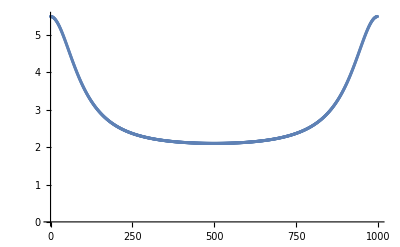

```mathematica
values={D1->1,D2->10,ω0->1,dt->0.3,M->999};
num1=Table[{k,meanPowerSpectrum[[1,1]]/(D1 dt^2)/.values},{k,0,M-1/.values}];
ListPlot[num1,AxesOrigin->{0,0}]
```

### Get the image of the deterministic part. Keep only terms for L[0], because everything else is ~O(1)

```mathematica
detImage=U.DiagonalMatrix[Map[K[#]&,λs]].Um1.R0+U.DiagonalMatrix[Map[L[#]&,λs]].Um1.a;
LKImages={K[λ1_]/;λ1===0:>0,
K[λ1_]/;λ1=!=0:>(dt (1-Exp[M λ1 dt])(Exp[λ1dt]-1))/(1-Exp[λ1 dt-2 π ⅈ k /M]),
L[λ1_]/;λ1===0:>M dt^2 δ[k],
L[λ1_]/;λ1=!=0:>(dt (1-Exp[M λ1 dt])(Exp[λ1dt]-1))/(1-Exp[λ1 dt-2 π ⅈ k /M])/λ1
};
detImage/.LKImages//Simplify
%//MatrixForm
```

{{(dt ⅇ^((2 ⅈ k π)/M-2 dt (-1+M) ω0) (-1+ⅇ^λ1dt) (-1+ⅇ^(2 dt M ω0)) (L+R01-R03))/(2 (-1+ⅇ^((2 ⅈ k π)/M+2 dt ω0)))},{(dt ⅇ^((2 ⅈ k π)/M-2 dt (-1+M) ω0) (-1+ⅇ^λ1dt) (-1+ⅇ^(2 dt M ω0)) (R02-R04))/(2 (-1+ⅇ^((2 ⅈ k π)/M+2 dt ω0)))},{-(dt ⅇ^((2 ⅈ k π)/M-2 dt (-1+M) ω0) (-1+ⅇ^λ1dt) (-1+ⅇ^(2 dt M ω0)) (L+R01-R03))/(2 (-1+ⅇ^((2 ⅈ k π)/M+2 dt ω0)))},{-(dt ⅇ^((2 ⅈ k π)/M-2 dt (-1+M) ω0) (-1+ⅇ^λ1dt) (-1+ⅇ^(2 dt M ω0)) (R02-R04))/(2 (-1+ⅇ^((2 ⅈ k π)/M+2 dt ω0)))}}

((dt ⅇ^((2 ⅈ k π)/M-2 dt (-1+M) ω0) (-1+ⅇ^λ1dt) (-1+ⅇ^(2 dt M ω0)) (L+R01-R03))/(2 (-1+ⅇ^((2 ⅈ k π)/M+2 dt ω0)))
(dt ⅇ^((2 ⅈ k π)/M-2 dt (-1+M) ω0) (-1+ⅇ^λ1dt) (-1+ⅇ^(2 dt M ω0)) (R02-R04))/(2 (-1+ⅇ^((2 ⅈ k π)/M+2 dt ω0)))
-(dt ⅇ^((2 ⅈ k π)/M-2 dt (-1+M) ω0) (-1+ⅇ^λ1dt) (-1+ⅇ^(2 dt M ω0)) (L+R01-R03))/(2 (-1+ⅇ^((2 ⅈ k π)/M+2 dt ω0)))
-(dt ⅇ^((2 ⅈ k π)/M-2 dt (-1+M) ω0) (-1+ⅇ^λ1dt) (-1+ⅇ^(2 dt M ω0)) (R02-R04))/(2 (-1+ⅇ^((2 ⅈ k π)/M+2 dt ω0))))

### Conclusion: the deterministic part does not have terms of order ~M, and is absent at all for the correct initial conditions

```mathematica
Clear[K]
```

```mathematica
K
```

K

```mathematica
K[1]
```

K[1]

```mathematica
K=10
```

10

```mathematica
K
```

K

```mathematica
(dt (-3 D1+D2+ⅇ^(4 dt ω0) (3 D1-D2)-2 ⅇ^(2 dt ω0) Cos[(2 k π)/M] ((3 D1-D2) Sinh[2 dt ω0])))/(4 ω0 (1+ⅇ^(4 dt ω0)-2 ⅇ^(2 dt ω0) Cos[(2 k π)/M]))//Simplify
```

((3 D1-D2) dt (-1+ⅇ^(4 dt ω0)) Sin[(k π)/M]^2)/(2 ω0 (1+ⅇ^(4 dt ω0)-2 ⅇ^(2 dt ω0) Cos[(2 k π)/M]))

```mathematica
(dt (-3 D1+D2+2 D1 dt ω0+2 D2 dt ω0+ⅇ^(4 dt ω0) (3 D1-D2+2 (D1+D2) dt ω0)-2 ⅇ^(2 dt ω0) Cos[(2 k π)/M] (2 (D1+D2) dt ω0+(3 D1-D2) Sinh[2 dt ω0])))/(4 ω0 (1+ⅇ^(4 dt ω0)-2 ⅇ^(2 dt ω0) Cos[(2 k π)/M]))-((3 D1-D2) dt (-1+ⅇ^(4 dt ω0)) Sin[(k π)/M]^2)/(2 ω0 (1+ⅇ^(4 dt ω0)-2 ⅇ^(2 dt ω0) Cos[(2 k π)/M]))//Simplify
```

1/2 (D1+D2) dt^2